# MATH7501 Practical 10 (Week 11), Semester 1-2021

## Topic: Sequences & Series, Limits and Derivatives

Author:  Aminath Shausan
Date: 14-05-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with units 5 to 8 contents  of the reading materials for MATH7501

# Resources

Chapters 5 to 8 of

https://en.wikipedia.org/wiki/Law_of_the_unconscious_statistician

# Section 1: Quiz 2

Do Quiz 2 of Sem1, 2021

See Quiz 2 solutions

# Section 2: Exponential Distribution

In probability theory and statistics, the exponential distribution is a continuous distribution that is commonly used to measure the expected time for an event to occur. For example,

in physics it is often used to measure radioactive decay,

in engineering it is used to measure the time associated with receiving a defective part on an assembly line,

in finance it is often used to measure the likelihood of the next default for a portfolio of financial assets.I

it can also be used to measure the likelihood of incurring a specified number of defaults within a specified time period.

If a random variable has the exponential distribution with parameter λ,we write it as: X ~ Exp(λ).

Here λ > 0 is called the rate parameter and X takes values in the interval [0, ∞).

The probability density function (pdf), f_X,  of X is given by:
                        f_X(x)= {λe^-λx , x ≥0
0,         x <0.

The cumulative distribution  function (cdf), F_X,  of X is given by:
                          F_X(x)= {1-e^-λx , x ≥0
0,             x <0.

Relationship between pdf and cdf of a continuous random variable
In general, suppose X is a continuous random variable defined on the entire real line, then we compute:

the probability of X falling within a given interval [a,b] is computed by integrating  its pdf, f_X.

```mathematica
P(a≤ X≤b) = ∫_a^b Subscript[f, X](x)dx
```

The cumulative distribution function (cdf), F_(X,) of X is defined as 
                     F_X(x) = P(-∞≤ X≤x) = ∫_(-∞)^x f_X(t)dt.

The pdf of a  continuous random variable X can be computed by differentiating its cdf, as long as the derivative exists:
                        f_X(x) = d/dx F_X(x).

Intuitively this means f_X(x)dx is the probability of X falling within the infinitesimal interval [x, x+dx]

Q1) Use the above general definition of cdf  to show that the cdf of X~Exp (λ) is given as in Eq (1)

```mathematica
Subscript[F, X](x) = P(0≤ X≤x) 
                           = ∫_0^x Subscript[f, X](t)dt
                           =∫_0^x λe^-λt dt    
                           = λ∫_0^x e^-λt dt   
                          =Subscript[λ[-1/λ e^-λt ], t=0]^(t=x)
                          ={{{1-e^-λx , x ≥0}, {0,             x <0}}
```

Q2) Plot the pdf and cdf of X~Exp (λ) for λ = 0.5, 1, 1.5, 2

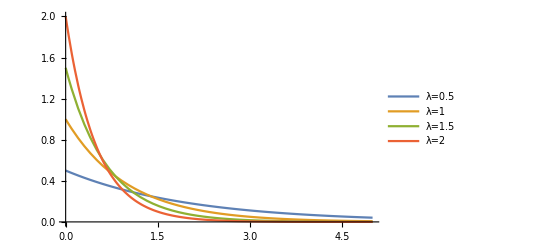

```mathematica
(* plot the pdf*)
Plot[Table[PDF[ExponentialDistribution[λ],x],{λ,{1/2,1,1.5,2}}]//Evaluate,
{x,0,5}, PlotRange->All, PlotLegends->{"λ=0.5", "λ=1", "λ=1.5", "λ=2"}]
```

```mathematica
(*plot the cdf*)
```

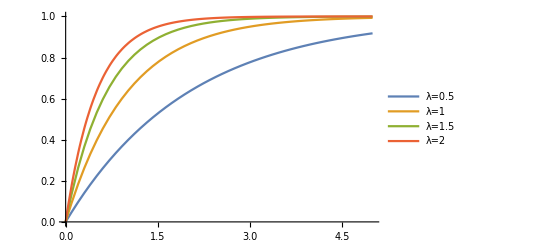

```mathematica
Plot[Table[CDF[ExponentialDistribution[λ],x],{λ,{1/2,1,1.5,2}}]//Evaluate,
{x,0,5}, PlotRange->All, PlotLegends->{"λ=0.5", "λ=1", "λ=1.5", "λ=2"}]
```

Mean and variance of a continuous random variable 
suppose X is a continuous random variable defined on the entire real line with pdf f_X(x), then

its mean , μ_X, is the expected value of X which is defined as follows
                 μ_X = E(X)  = ∫_(-∞)^∞ xf_X(x)dx

and  variance of X, (σ^2)_X, is  the  expected variability of X form its mean, μ_X. Variance of X is computed as

```mathematica
Subscript[σ^2, X]=var(X) =E[(X-Subscript[μ, X])^2]
                                                   =E[X^2-2 Subscript[μ, X] X +Subscript[μ, X]^2], after expanding (X-mu)^2
                                                  =E[X^2]-2 Subscript[μ, X] E[X] +Subscript[μ, X]^2  , after using the peoperty : E(aX+bY) = aE(X) +bE(Y) for two random variables X and Y
                                                  = E[X^2]-2 Subscript[μ, X]^2 +Subscript[μ, X]^2, using the fact that E[X] = Subscript[μ, X]
                                                  =E[X^2]-(Subscript[μ, X]^2)  ---------------------------- Eq (2)
```

```mathematica
Note that X^2 is a function of X (say g(X)= X^2) . Then by the law of the unconscious statistician for continuous random variable, we have  E[X^2] = ∫_(-∞)^∞ x^2 Subscript[f, X](x)dx. Thus Eq (2) is computed as: 
                     Subscript[σ^2, X]=∫_(-∞)^∞ x^2 Subscript[f, X](x)dx-(Subscript[μ, X]^2).
```

Q3) Show that  the mean of X ~ Exp(λ) = 1/λ

```mathematica
Subscript[μ, X] = E(X)  = ∫_0^∞ xλe^-λx dx
                                                 =λ∫_0^∞ xe^-λx dx
                                                 = λ/λ{[-xe^-λx]_(x=0)^(x=∞) + ∫_0^∞ e^-λx dx}, 
using integration bi parts : ∫f(x)g'(x)dx = f(x)g(x) - ∫f'(x)g(x)dx, where f(x) = x and g'(x) =  ∫_0^∞ e^-λx
                                              = {0 -Subscript[(1/λ)[e^-λx], x=0]^(x=∞)}
                                             = 1/λ
```

Q4)Show that the variance of X~ Exp(λ) = 1/λ^2

To compute  (σ^2)_X=∫_(-∞)^∞ x^2 f_X(x)dx-μ_X^2, first we need to find

```mathematica
∫_(-∞)^∞ x^2 Subscript[f, X](x) = ∫_0^∞ x^2 λe^-λx dx
                                              =λ∫_0^∞ x^2 e^-λx dx
                                             = λ/λ{[-x^2 e^-λx]_(x=0)^(x=∞) + 2∫_0^∞ xe^-λx dx},
```

```mathematica
using integration bi parts with f(x) = x^2 and g'(x) =  ∫_0^∞ e^-λx
                                           = {0 +2/λ∫_0^∞ xλe^-λx dx}, multiplying by λ/λ
                                        = 2/λ E[X]
                                       = 2/λ^2
Thus 
                                   Subscript[σ^2, X]= 2/λ^2 -(1/λ)^2 
                                           = 1/λ^2
```